```mathematica
τ["in"]=2.;τ["out"]=30.;τ["open"]=300.;τ["close"]=500.;
```

```mathematica
vc=0.13;
```

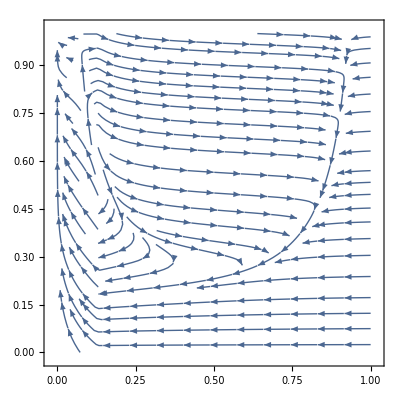

```mathematica
StreamPlot[{(h v^2(1-v))/τ["in"]-v/τ["out"],Dot@@MapAt[Boole,Internal`FromPiecewise[Piecewise[{{(1-h)/τ["open"],v<vc},{-h/τ["close"],v≥vc}}]],1]},{v,0,1},{h,0,1}]
```

```mathematica
j[t_]:=If[Mod[t,2500]<1,0.8,0]
```

```mathematica
fv=Compile[{{h,_Real},{v,_Real},{t,_Real}},(h v^2(1-v))/τ["in"]-v/τ["out"]+j[t]];vrhs[h_?NumericQ,v_?NumericQ,t_?NumericQ]:=fv[h,v,t];
```

```mathematica
fh=Compile[{{h,_Real},{v,_Real}},Piecewise[{{(1-h)/τ["open"],v<vc},{-h/τ["close"],v≥vc}}]];hrhs[h_?NumericQ,v_?NumericQ]:=fh[h,v]
```

```mathematica
s=NDSolve[{v'[t]==vrhs[h[t],v[t],t],h'[t]==hrhs[h[t],v[t]],v[0]==0.5,h[0]==1.0},{v[t],h[t]},{t,0,5000},StartingStepSize->0.001,Method->{"FixedStep",Method->{"ExplicitEuler"}}]
```

{{v[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],h[t]→InterpolatingFunction[{{0., 5000.}}, <>][t]}}

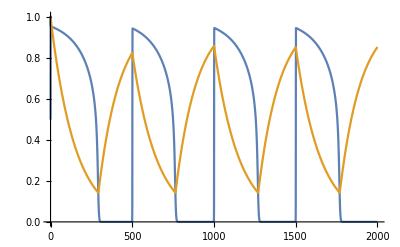

```mathematica
Plot[Evaluate[{v[t],h[t]}/.s],{t,0,2000}]
```

```mathematica
AbsoluteTiming[NDSolve[{v'[t]==vrhs[h[t],v[t],t],h'[t]==hrhs[h[t],v[t]],v[0]==0.5,h[0]==1.0},{v[t],h[t]},{t,0,5000},StartingStepSize->0.001,Method->{"FixedStep",Method->{"ExplicitEuler"}}]]
```

{157.65,{{v[t]→InterpolatingFunction[{{0., 5000.}}, <>][t],h[t]→InterpolatingFunction[{{0., 5000.}}, <>][t]}}}

```mathematica
sx=NDSolve[{v'[t]==(h[t] v[t]^2(1-v[t]))/τ["in"]-v[t]/τ["out"]+j[t],h'[t]==Piecewise[{{(1-h[t])/τ["open"],v[t]<vc},{(-h[t])/τ["close"],True}}],v[0]==0.5,h[0]==1.0},{v[t],h[t]},{t,0,600000}]
```

{{v[t]→InterpolatingFunction[{{0., 600000.}}, <>][t],h[t]→InterpolatingFunction[{{0., 600000.}}, <>][t]}}

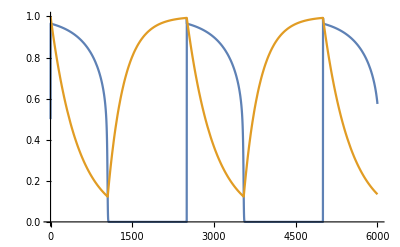

```mathematica
Plot[Evaluate[{v[t],h[t]}/.sx],{t,0,6000}]
```

```mathematica
AbsoluteTiming[un=NDSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],(D[u[x,t],x]/.x->0)==0,(D[u[x,t],x]/.x->4)==0,u[x,0]==Piecewise[{{Exp[-1/(1-(x-2)^2)],1<x<3},{0,True}}]},u,{x,0,4},{t,0,2}]]
```

{0.0986396,{{u→InterpolatingFunction[{{0., 4.}, {0., 2.}}, <>]}}}

```mathematica
AbsoluteTiming[un=NDSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],(D[u[x,t],x]/.x->0)==0,(D[u[x,t],x]/.x->4)==0,u[x,0]==Exp[-(x-2)^2]},u,{x,0,4},{t,0,10}]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{0.0195507,{{u→InterpolatingFunction[{{0., 4.}, {0., 10.}}, <>]}}}

```mathematica
AbsoluteTiming[un=NDSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],(D[u[x,t],x]/.x->0)==0,(D[u[x,t],x]/.x->4)==0,u[x,0]==Exp[-(x-2)^2]},u,{x,0,4},{t,0,2}]]
```

```mathematica
Plot3D[Evaluate[u[x,t]/.un],{t,0,2},{x,0,4}, PlotRange->All,AxesLabel->{"t","x"}]
```

-Graphics3D-

```mathematica
Animate[Plot[Evaluate[u[x,t]/.un],{x,0,4},PlotRange->{0,1}],{t,0,2},AnimationRunning->False]
```